```mathematica
(* valna funkcija za elektron u jami *)
<<PhysicalConstants`
m =1; l=1;
Energija[n_]:= PlanckConstantReduced^2 n^2/(8 m l^2)
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Plot[Energija[n],{n,1,3}]
```

-Graphics-

```mathematica
Energija[2]
```

5.56061×10^-69 Joule^2 Second^2

2

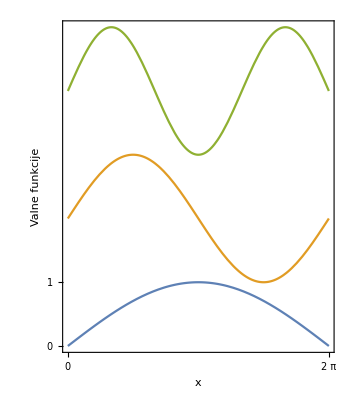

```mathematica
a=2
Plot[{Sin[1/2x],Sin[2/2x]+a,Sin[3/2x]+2a},{x,0,2 π},Frame->True,FrameTicks->{{0,2 Pi},{0,1}},AspectRatio->1.2,FrameLabel->{"x","Valne funkcije"}]
```

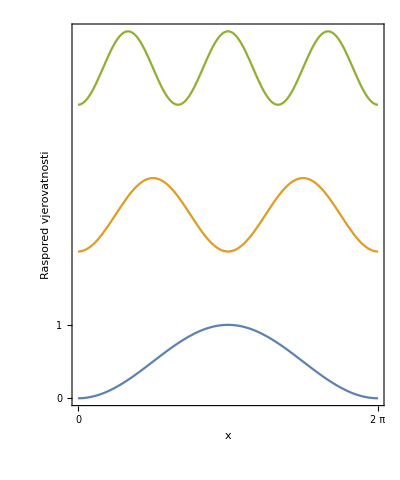

```mathematica
Plot[{Sin[1/2x]^2,Sin[2/2x]^2+a,Sin[3/2x]^2+2a},{x,0,2 π},Frame->True,FrameTicks->{{0,2 Pi},{0,1}},AspectRatio->1.2,FrameLabel->{"x","Raspored vjerovatnosti"}]
```

```mathematica
β = 10;fun[z_] := Cos[z] + β Sin[z]/z;
```

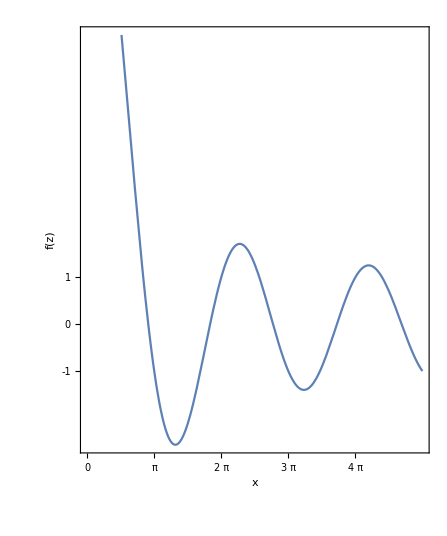

```mathematica
funz =Plot[fun[z],{z,0, 5π},Frame->True,FrameTicks->{{0,Pi,2 Pi, 3 Pi,4 Pi},{-1,0,1}},AspectRatio->1.2,FrameLabel->{"x","f(z)"},GridLines->{{2.6276754329857965,Pi,5.3073247991181285,6.283185307179586,2Pi,8.067135580679963,3Pi,10.90870750976562,4Pi,13.8192},{-1,1}}]
```

```mathematica
FindRoot[fun[z] == 1,{z,4.5Pi}]
```

{z→13.8192}

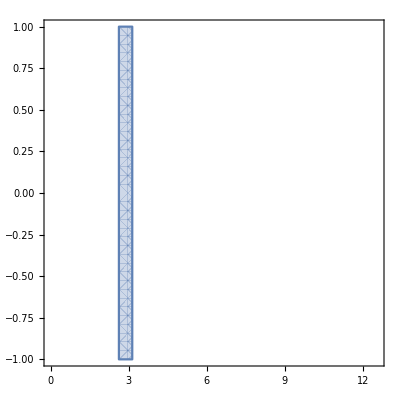

```mathematica
reg =RegionPlot[2.6276754329857965≤ x≤ Pi && y ≥ -1,{x,0,4 Pi},{y,-1,1}]
```

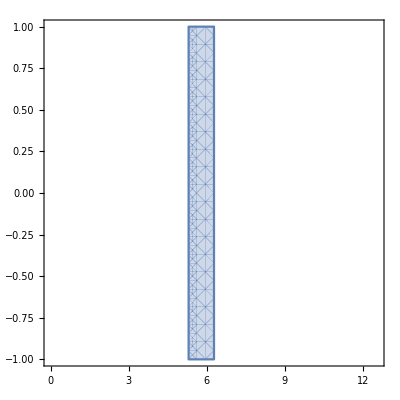

```mathematica
reg1=RegionPlot[ 5.3073247991181285≤ x ≤ 2Pi && y ≥ -1,{x,0,4 Pi},{y,-1,1}]
```

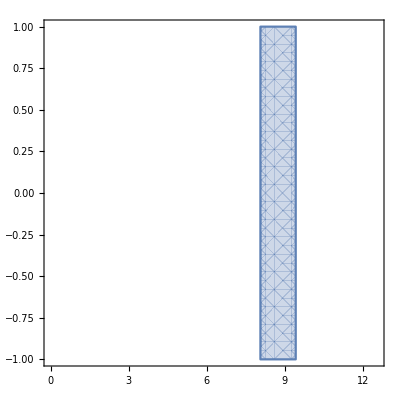

```mathematica
reg2=RegionPlot[ 8.067135580679963≤ x ≤ 3Pi && y ≥ -1,{x,0,4 Pi},{y,-1,1}]
```

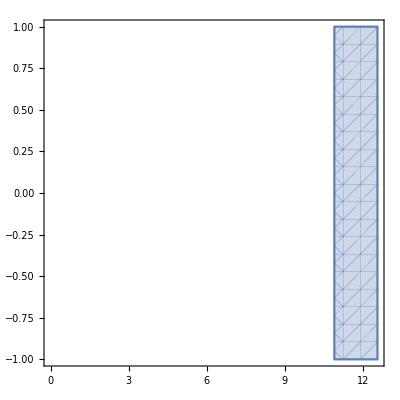

```mathematica
reg3=RegionPlot[ 10.90870750976562≤ x ≤ 4Pi && y ≥ -1,{x,0,4 Pi},{y,-1,1}]
```

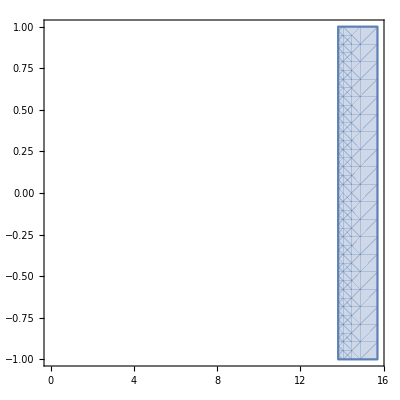

```mathematica
reg4=RegionPlot[ 13.8192≤ x ≤ 5Pi && y ≥ -1,{x,0,5 Pi},{y,-1,1}]
```

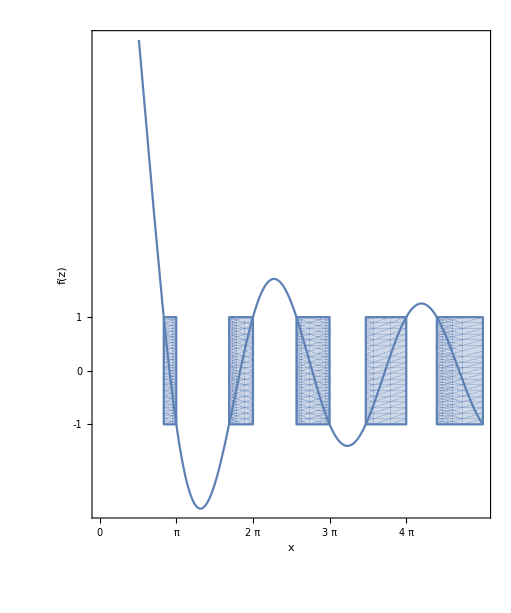

```mathematica
Show[{funz,reg,reg1,reg2,reg3,reg4}]
```

```mathematica
m = Quantity["ElectronMass"];
h = Quantity["ReducedPlanckConstant"]
Energija[k_]:=h^2 k^2/(2*m)
```

1 ℏ

```mathematica
Energija[1Pi]//N
```

4.9348 ℏ^2/m_e

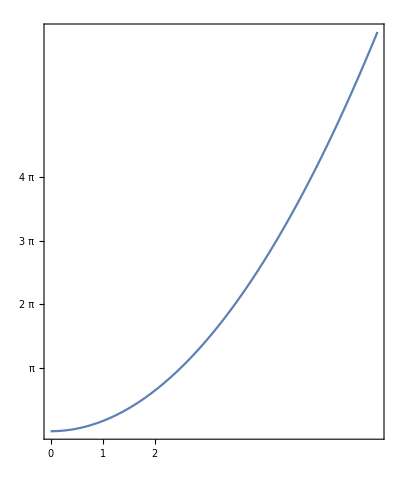

```mathematica
Plot[Energija[k],{k,0,2Pi},Frame->True,FrameTicks->{{0,1,2},{1Pi,2Pi,3Pi,4Pi}},GridLines->{{4.9348,2Pi/ar,3Pi/ar,4Pi/ar},{2.6276754329857965,Pi,5.3073247991181285,6.283185307179586,2Pi,8.067135580679963,3Pi,10.90870750976562,4Pi,13.8192}},AspectRatio->1.2]
```

Ovo je  β = m α a/h^2  za energiju dok je ω =

```mathematica
ω = Sqrt[2 m Energija[k]/h^2]; α = 1;
a = h^2 β /m α;
```

```mathematica
a
```

10 ℏ^2/m_e

```mathematica
QuantityMagnitude[Quantity[100,("ReducedPlanckConstant")^2/("ElectronMass")]]
```

100

```mathematica
UnitConvert[Quantity[100,("ReducedPlanckConstant")^2/("ElectronMass")],"SI"]
```

1.22085286×10^-36 kg m^4/s^2

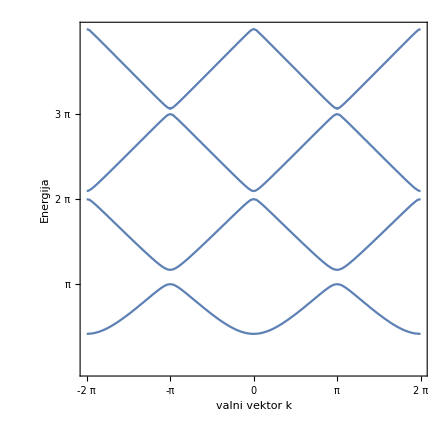

```mathematica
ContourPlot[Cos[q] == Cos[k]+Sin[k]/k ,{q,-2Pi,2Pi},{k,0,4Pi},FrameTicks->{{-π,-2π,0π,π,2π},{π,2π,3π}},FrameLabel->{"valni vektor k","Energija"}]
```

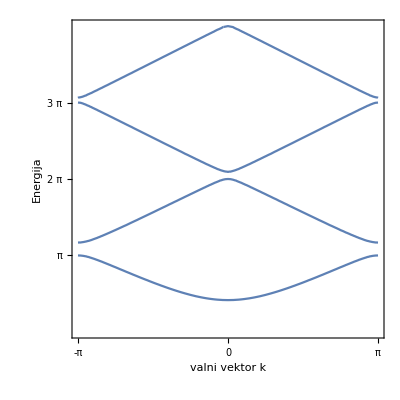

```mathematica
ContourPlot[Cos[q] == Cos[k]+Sin[k]/k ,{q,-Pi,Pi},{k,0,4Pi},FrameTicks->{{-π,-2π,0π,π,2π},{π,2π,3π}},FrameLabel->{"valni vektor k","Energija"}]
```

```mathematica
ContourPlot[Cos[q] == Cos[k]+Sin[k]/k ,{q,-Pi,Pi},{k,0,1.1Pi},FrameTicks->{{-π,-2π,0π,π,2π},{π,2π,3π}},FrameLabel->{"valni vektor k","Energija"}]
```

```mathematica
ContourPlot[Cos[q] == Cos[k]+Sin[k]/k ,{q,-Pi,Pi},{k,0,1.1Pi},FrameTicks->{{-π,-2π,0π,π,2π},{π,2π,3π}},FrameLabel->{"valni vektor k","Energija"}]
```